```mathematica
ClearAll["Global`*"]
```

# Feature Distribution Visualization

In this Notebook, we will create visualizations of the distributions for features for the various counties. The purpose of these visualizations is to further understand how these features are distributed..

## Data Import

Here we will import the time-series data and the compiled data that will be used for the machine learning models.

## File Paths

```mathematica
hereDir=NotebookDirectory[];
projDir=ParentDirectory[hereDir];
compDataFile=FileNameJoin[{projDir,"RawDataToUsableDataConverter","src","FinalCombinedFeaturesWithSeverity.csv"}];
```

## Imported Data

The compiled data has information in the following order:
1. COVID Severity Index
2. FIPS County Code
3. Total Votes (2016)
4. Votes for Democratic Candidate (2008)
5. Votes for Democratic Candidate (2012)
6. Votes for Republican Candidate (2008)
7. Votes for Republican Candidate (2012)
8. Percentage of Votes for Democratic Candidate (2016)
9. Percentage of Votes for Republican Candidate (2016)
10. Percentage of Votes for Republican Candidate (2012)
11. Percentage of Votes for Republican Candidate (2008)
12. Percentage of Votes for Democratic Candidate (2012)
13. Percentage of Votes for Democratic Candidate (2008)
14. Percentage of Adults with Less Than a High School Diploma (Exit Poll 2016 Election)
15. Percentage of Adults with at Least a High School Diploma (Exit Poll 2016 Election)
16. Percentage of Adults with at Least a Bachelor’s Degree (Exit Poll 2016 Election)
17. Percentage of Adults with at Least a Graduate Degree (Exit Poll 2016 Election)
18. School Enrollment (???)
19. Percentage of Children Under 6 Living in Poverty (2016 Estimate)
20. Percentage of Adults 65 and Older Living in Poverty (2016 Estimate)
21. Total Population (2016 Estimate)
22. Poverty Rate Below Federal Poverty Threshold (2016 Estimate)
23. Percentage of People in Management, Professional, and Related Occupations (2016 Estimate)
24. Percentage of People in Service Occupations (2016 Estimate)
25. Percentage of People in Sales and Office Occupations (2016 Estimate)
26. Percentage of People in Farming, Fishing, and Forestry Occupations (2016 Estimate)
27. Percentage of People in Construction, Extraction, Maintenance, and Repair Occupations (2016 Estimate)
28. Percentage of People in Production, Transportation, and Material Moving Occupations (2016 Estimate)

```mathematica
compData=Import[compDataFile,"Table","FieldSeparators"->";"];
```

## Feature Distribution Visualization

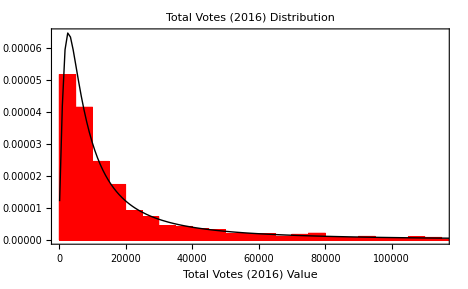

```mathematica
featureIndex=3;
featureNameList={"COVID Severity Index","FIPS County Code","Total Votes (2016)","Votes for Democratic Candidate (2008)","Votes for Democratic Candidate (2012)","Votes for Republican Candidate (2008)","Votes for Republican Candidate (2012)","Percentage of Votes for Democratic Candidate (2016)","Percentage of Votes for Republican Candidate (2016)","Percentage of Votes for Republican Candidate (2012)","Percentage of Votes for Republican Candidate (2008)","Percentage of Votes for Democratic Candidate (2012)","Percentage of Votes for Democratic Candidate (2008)","Percentage of Adults with Less Than a High School Diploma (Exit Poll 2016 Election)","Percentage of Adults with at Least a High School Diploma (Exit Poll 2016 Election)","Percentage of Adults with at Least a Bachelor's Degree (Exit Poll 2016 Election)","Percentage of Adults with at Least a Graduate Degree (Exit Poll 2016 Election)","School Enrollment (???)","Percentage of Children Under 6 Living in Poverty (2016 Estimate)","Percentage of Adults 65 and Older Living in Poverty (2016 Estimate)","Total Population (2016 Estimate)","Poverty Rate Below Federal Poverty Threshold (2016 Estimate)","Percentage of People in Management, Professional, and Related Occupations (2016 Estimate)","Percentage of People in Service Occupations (2016 Estimate)","Percentage of People in Sales and Office Occupations (2016 Estimate)","Percentage of People in Farming, Fishing, and Forestry Occupations (2016 Estimate)","Percentage of People in Construction, Extraction, Maintenance, and Repair Occupations (2016 Estimate)","Percentage of People in Production, Transportation, and Material Moving Occupations (2016 Estimate)"};

featureOfInterest=compData[[;;,featureIndex]];

barChart=Histogram[featureOfInterest,Automatic,"PDF",
Axes->False,
Frame->{{True,False},{True,False}},
PlotLabel->StringJoin[featureNameList[[featureIndex]]," Distribution"],
FrameLabel->{{,},{StringJoin[featureNameList[[featureIndex]]," Value"],}},
ChartStyle->Directive[Red],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times"],
ImageSize->(72*6.5)
];

estimatedDist=FindDistribution[featureOfInterest,TargetFunctions->"Continuous"];
distPlot=Plot[PDF[estimatedDist,x],{x,Min[featureOfInterest]-10,Max[featureOfInterest]},
PlotRange->All,
Axes->False,
Frame->{{True,False},{True,False}},
PlotLabel->StringJoin[featureNameList[[featureIndex]]," Distribution"],
FrameLabel->{{,},{StringJoin[featureNameList[[featureIndex]]," Value"],}},
PlotStyle->Directive[Black,Thick],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times"],
ImageSize->(72*6.5)
];

Show[barChart,distPlot]
```